```mathematica
Import["ob.nb","nb"]
Import["operators.nb","nb"]
Import["mews_and_alphas.nb","nb"]
```

```mathematica
(* QUARK MASSES *)
uq=0.2848 (* up quark *);
sq=0.5553 (* strange quark *);
cq=1.8182 (* charm quark *);
bq=5.2019 (* bottom quark *);
```

```mathematica
(* set masses and maximum energy (γMax) and build the transformation matrices *)
baryonMass[gammaMax_,Lambda_,mass1_,mass2_,mass3_]:=(
γMax=gammaMax;
Λ=Lambda;
m1=mass1;
m2=mass2;
m3=mass3;
t1=tMatrix[Λ,gammaMax,1]; (* transformation matrix 1 *)
t2=tMatrix[Λ,gammaMax,2];(* transformation matrix 2 *)
size=Dimensions[t1][[1]]; (* size of matrix *)
sigma=0.154/2; (* coefficient of string strength term *)
alphaCoulomb=0.0175; (* coefficient of Coulomb term *)
Cqqq=-1.4204  (* V = -Subscript[α, C]/r + σr + Subscript[C, qqq] *);
Min[Table[Eigenvalues[baryonHamiltonian[ω]][[-1]],{ω,0.1,0.6,0.01}]])
```

```mathematica
γMax=6;
Λ=0;
m1=1;
m2=1;
m3=1;
t1=tMatrix[0,6,1];
t2=tMatrix[0,6,2];
size=Dimensions[t1][[1]];
```

20

```mathematica
baryonList={{uq,uq,uq},{uq,uq,cq},{uq,uq,bq},{uq,sq,cq},{uq,sq,bq},{uq,cq,cq},{uq,cq,bq},{uq,bq,bq},{bq,cq,cq},{cq,cq,cq},{bq,bq,cq},{bq,bq,bq}};
```

```mathematica
For[index=1,index≤Length[baryonList],index++,
Print[index];
Print[baryonList[[index,1]]];
Print[baryonList[[index,2]]];
Print[baryonList[[index,3]]];
Print[Table[baryonMass[γMax,1,baryonList[[index,1]],baryonList[[index,2]],baryonList[[index,3]]],{γMax,1,7,2}]]]
```

```mathematica
(* BARYON *)
baryonHamiltonian[ω_]:=(
omega=ω;
vCoulomb=polynomialOperator[Λ,γMax,-1];
vLinear=polynomialOperator[Λ,γMax,1];
v12baryon=-alphaCoulomb*α*vCoulomb+(sigma*vLinear)/α;
v23baryon=-alphaCoulomb*α1*(Transpose[t1].vCoulomb.t1)+(sigma*(Transpose[t1].vLinear.t1))/α1;
v31baryon=-alphaCoulomb*α2*(Transpose[t2].vCoulomb.t2)+(sigma*(Transpose[t2].vLinear.t2))/α2;
kin=kMatrix[Λ,γMax,ω];
mas1=IdentityMatrix[size]*m1;
mas2=IdentityMatrix[size]*m2;
mas3=IdentityMatrix[size]*m3;
cqqq=IdentityMatrix[size]*(Cqqq);
Hbaryon=mas1+mas2+mas3+kin+v12baryon+v23baryon+v31baryon+cqqq)
```

```mathematica
Eigenvalues[baryonHamiltonian[0.36]]
```

{1.821,1.821,1.77369,1.12457}

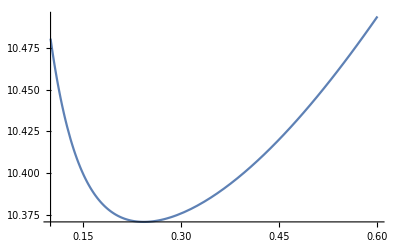

{{5.93237,0.1},{5.90381,0.11},{5.88171,0.12},{5.86459,0.13},{5.8513,0.14},{5.84101,0.15},{5.83305,0.16},{5.8269,0.17},{5.82215,0.18},{5.81851,0.19},{5.8157,0.2},{5.81355,0.21},{5.8119,0.22},{5.81062,0.23},{5.80964,0.24},{5.80889,0.25},{5.8083,0.26},{5.80784,0.27},{5.80749,0.28},{5.80721,0.29},{5.807,0.3},{5.80684,0.31},{5.80672,0.32},{5.80664,0.33},{5.80661,0.34},{5.8066,0.35},{5.80663,0.36},{5.8067,0.37},{5.80681,0.38},{5.80695,0.39},{5.80714,0.4},{5.80738,0.41},{5.80766,0.42},{5.808,0.43},{5.80839,0.44},{5.80884,0.45},{5.80935,0.46},{5.80992,0.47},{5.81055,0.48},{5.81125,0.49},{5.81202,0.5},{5.81286,0.51},{5.81377,0.52},{5.81476,0.53},{5.81582,0.54},{5.81695,0.55},{5.81816,0.56},{5.81944,0.57},{5.8208,0.58},{5.82224,0.59},{5.82375,0.6}}

```mathematica
Plot[Eigenvalues[baryonHamiltonian[ω]][[-1]],{ω,0.1,0.6}]
```

```mathematica
(* SHO *)
ω=1;
ρ1=Cos[-theta[1]]*ρ-Sin[-theta[1]]*λ;
ρ2=Cos[-theta[2]]*ρ-Sin[-theta[2]]*λ;
v=1/2(μρ ρ^2)/α^2+1/2(μ1 ρ1^2)/α1^2+1/2(μ2 ρ2^2)/α2^2;
potential=Collect[Expand[v],ρ*λ]//Chop;
coeffRho=Coefficient[potential,ρ^2];
coeffLam=Coefficient[potential,λ^2];
kin=kMatrix[Λ,γMax,ω];
vOscillator=polynomialOperator[Λ,γMax,2];
v12sho=(μρ ω^2)/(2 α^2)vOscillator;
v23sho=(μ1 ω^2)/(2 α1^2)Transpose[t1].vOscillator.t1;
v31sho=(μ2 ω^2)/(2 α2^2)Transpose[t2].vOscillator.t2;
vExct=vExact[Λ,γMax,coeffRho,coeffLam];
HamiltonianTalmi=kin+v12sho+v23sho+v31sho;
HamiltonianExact=kin+vExct;
Eigenvalues[HamiltonianExact*1.]
Eigenvalues[HamiltonianTalmi]
eVecTalmi=Eigenvectors[HamiltonianTalmi];
eVecExact=Eigenvectors[HamiltonianExact];
(* testing expected values <T> should be equal to <V> *)
kExpected=eVecTalmi[[-1]].(kin).eVecTalmi[[-1]];
vExactExpected=eVecTalmi[[-1]].(vExct).eVecTalmi[[-1]];
vTalmiExpected=eVecTalmi[[-1]].(Chop[v12sho+v23sho+v31sho]).eVecTalmi[[-1]];
dim;
```

```mathematica
energy[n_,l_,N_,L_]:=2/(√3)(2n+l+3/2)+√(5/3)(2N+L+3/2)
```

```mathematica
energy[0,1,0,0]*1.
```

4.82324

```mathematica
(* COMBINATIONS OF NON-ZERO TALMI MOSHINSKY TRANSFORMATIONS *)
(* |Subscript[n, ρ] Subscript[l, ρ](ρ),Subscript[n, λ] Subscript[l, λ](λ):Λ> = ∑ Talmi-coeff x |NL(ρ')nl(λ'):Λ> , SHOWING ONLY NON-ZERO TERMS *)
(*bra=talmiCoeffs[0,0,0,0,0,1];
ket=talmiCoeffs[0,0,1,0,0,1];
(* only combinations with L'=L, n'=n and l'=l survive ( < N'L'n'l' : Λ | V(√2 ρ') | NLnl : Λ >)*)
combs={};
For[Bvec=1,Bvec≤Length[bra],Bvec++,
For[Kvec=1,Kvec≤Length[ket],Kvec++,
If[bra[[Bvec,2,3]]==ket[[Kvec,2,3]],
If[bra[[Bvec,2,4]]==ket[[Kvec,2,4]],
If[bra[[Bvec,2,2]]==ket[[Kvec,2,2]],
AppendTo[combs,{bra[[Bvec,1]]*ket[[Kvec,1]],bra[[Bvec,2]],ket[[Kvec,2]]}]
]]]]]
combs*)
```

```mathematica
a1
```

-1/2

```mathematica
a2
```

-1/2